```mathematica
foldname="C:\\Users\\msztr\\OneDrive\\Documents\\GitHub\\VeriGudGame\\Measurements\\Empty"
filenms = FileNames[All,foldname];
```

C:\Users\msztr\OneDrive\Documents\GitHub\VeriGudGame\Measurements\Empty

```mathematica
samplerate=50 10^6;
```

```mathematica
res=Table[dat=Import[filenms[[i]]][[5;;-1]];
dat1={#[[1]]/samplerate,#[[2]]}&/@dat[[All,1;;2]];
dat2={#[[1]]/samplerate,#[[2]]}&/@dat[[All,{1,3}]];
fit1 = NonlinearModelFit[dat1, a Sin[b t+ c] + d  , {{a,Max[dat1[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat1,Last][[1,1]]/Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
fit2 = NonlinearModelFit[dat2, a Sin[b t+ c] + d , {{a,Max[dat2[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat2,Last][[1,1]]/Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
Flatten[{Transpose[{fit1["BestFitParameters"][[All,2]],fit1["ParameterErrors"]}],Transpose[{fit2["BestFitParameters"][[All,2]],fit2["ParameterErrors"]}]}],{i,1,Length[filenms]}]
Export[foldname<>"_results.xlsx",res]
```

{{0.0376626,0.000256615,942317.,751.814,-0.200301,0.0132437,0.00614747,0.000180192,2.49856,0.00125126,942468.,58.7745,4.52763,0.00102803,0.00724578,0.000893285},{-0.039595,0.000255753,973919.,692.092,21.3057,0.0122326,0.00822393,0.000178846,2.49922,0.00126162,973881.,61.6142,4.05249,0.00107316,0.00634188,0.000909202},{0.0417129,0.000261553,1.00507×10^6,688.821,17.6873,0.0121317,0.00691759,0.000184457,-2.49823,0.00134672,1.0053×10^6,64.467,6.71371,0.00112604,0.00668372,0.000963931},{0.0437614,0.000256894,1.0363×10^6,683.069,10.9303,0.0119432,0.00651625,0.000183881,-2.49903,0.00145554,1.0367×10^6,65.7589,6.23626,0.00115679,0.00770991,0.0010261},{0.0462302,0.000252126,1.0681×10^6,662.693,4.15566,0.0115327,0.00741644,0.000182166,-2.49905,0.0015385,1.06815×10^6,66.4992,5.75444,0.00117611,0.00582133,0.0010739},{0.0488188,0.000256381,1.09925×10^6,632.237,3.67931,0.011014,0.00783273,0.000184199,2.49915,0.0015973,1.09957×10^6,69.1655,8.41508,0.00122269,0.00722191,0.00111656},{0.0520312,0.000255861,1.13123×10^6,562.525,3.1871,0.00985737,0.00851954,0.000181135,2.49822,0.00166037,1.13098×10^6,75.1582,7.93825,0.00132088,0.00893899,0.00117355},{-0.0545518,0.000262305,1.16292×10^6,525.304,5.85052,0.00926259,0.00716578,0.00018382,2.49943,0.00165076,1.16238×10^6,78.5148,1.17843,0.00137154,0.00652033,0.0011814},{-0.0582832,0.000268915,1.19382×10^6,500.919,11.6569,0.00884329,0.00926623,0.000188561,2.49916,0.00161745,1.19381×10^6,77.9562,0.699514,0.00136001,0.00739974,0.00116062},{0.062097,0.000265016,1.22512×10^6,479.884,8.03061,0.00843997,0.00848913,0.00018766,-2.49921,0.00166638,1.22518×10^6,77.6514,3.35822,0.00136003,0.00724529,0.00118431},{0.0657676,0.00026868,1.25647×10^6,482.006,32.6822,0.00842813,0.00723707,0.000192527,-2.49947,0.00178788,1.25664×10^6,79.3678,2.8799,0.00139854,0.00689902,0.0012555},{0.0703557,0.000260755,1.28814×10^6,446.27,0.772396,0.00777807,0.00882278,0.000187494,-2.50102,0.00174453,1.288×10^6,75.6303,2.39946,0.0013367,0.00778667,0.00121918},{-0.0750376,0.000262453,1.3194×10^6,411.006,9.71529,0.0071739,0.00607525,0.000187148,2.49995,0.00175149,1.31942×10^6,77.3688,5.06195,0.00136433,0.00669995,0.00123013},{0.0803078,0.000268414,1.35098×10^6,375.284,37.5096,0.00658614,0.00773257,0.000189159,2.49928,0.00179912,1.3509×10^6,83.0819,4.58616,0.0014568,0.00765621,0.00127758},{-0.0867117,0.000267422,1.38259×10^6,336.757,2.45904,0.00593761,0.00731848,0.000187429,2.49947,0.00177735,1.3823×10^6,84.8187,4.10844,0.00148132,0.00663615,0.00127243},{0.0934953,0.000265945,1.41375×10^6,313.701,5.11662,0.0055356,0.00798178,0.000187104,2.49901,0.00187018,1.41375×10^6,88.6796,3.6282,0.00154982,0.00663451,0.00133567},{0.101806,0.000257567,1.44507×10^6,289.863,4.62513,0.00509787,0.00822206,0.000183018,-0.498168,0.0633272,1.73801×10^6,14207.4,4.97694,0.250139,0.00793139,0.0445905},{0.111361,0.0002705,1.47644×10^6,288.103,4.13267,0.00504087,0.00735322,0.000193777,2.49857,0.00204393,1.47653×10^6,89.9855,8.94946,0.00158707,0.00682311,0.00143273},{0.0268866,0.00313426,1.79856×10^6,12853.8,2.35887,0.226387,0.00376435,0.00220061,2.49889,0.00211177,1.50797×10^6,92.4683,8.47662,0.0016324,0.00885658,0.00147923},{-0.135886,0.000286511,1.53942×10^6,242.74,6.27914,0.00423647,0.00647583,0.000203161,2.4969,0.00218925,1.53938×10^6,98.6853,7.99198,0.00173635,0.00705883,0.0015445},{0.152378,0.000300376,1.5706×10^6,219.167,8.92417,0.00384369,0.00764291,0.00021123,2.49543,0.00213327,1.5708×10^6,99.9817,1.23294,0.00175059,0.00781899,0.0015195},{0.173272,0.00032067,1.60235×10^6,203.616,8.4045,0.00359142,0.00798876,0.000225182,2.49483,0.00218446,1.60222×10^6,104.043,0.751534,0.00181777,0.00789135,0.00156175},{0.199721,0.000322716,1.63366×10^6,181.405,33.0238,0.00320861,0.00774915,0.000227922,0.518797,0.0635338,1.92458×10^6,13531.1,-1.00767,0.238578,0.00737043,0.0446008},{0.234914,0.000340268,1.66499×10^6,167.779,1.07343,0.00296119,0.00748359,0.000242196,0.496516,0.0624691,1.9605×10^6,14305.1,-1.55904,0.251375,0.00607781,0.0441697},{0.257044,0.000345723,1.68075×10^6,157.356,0.793477,0.00276906,0.0075921,0.000246618,-0.499785,0.061851,1.97887×10^6,14327.2,1.3022,0.251193,0.00824405,0.0439305},{0.283436,0.0003659,1.69638×10^6,151.42,0.509539,0.00265416,0.00758655,0.000261055,0.512377,0.0613428,1.99653×10^6,14038.7,-2.11139,0.245725,0.00600975,0.0437082},{-0.314749,0.000387139,1.71213×10^6,143.615,34.7753,0.00250625,0.00731767,0.00027575,2.47463,0.00235341,1.71215×10^6,104.471,5.36042,0.00184342,0.0084841,0.00164982},{0.352279,0.000413088,1.72792×10^6,135.599,56.458,0.00235675,0.00870865,0.000293405,2.46667,0.00223847,1.72788×10^6,100.53,5.12253,0.00177222,0.00767662,0.00157268},{0.078468,0.00931801,2.02818×10^6,13392.1,-1.58542,0.236554,0.0181264,0.00657959,0.555341,0.060846,2.03434×10^6,12825.6,3.60001,0.22443,0.0080247,0.0433188},{0.386852,0.000441197,1.74043×10^6,130.754,18.4912,0.00226703,0.00803385,0.000312656,0.560775,0.0608661,2.04002×10^6,12658.1,3.50781,0.221566,0.0065975,0.0432893},{0.0871119,0.0102603,2.04186×10^6,13387.4,-1.89763,0.237219,0.0198793,0.00725913,0.564893,0.0608686,2.04565×10^6,12512.2,3.42999,0.219148,0.00791778,0.0432412},{0.428259,0.000476296,1.75301×10^6,126.782,55.9201,0.00219581,0.00650507,0.00033705,0.568291,0.060895,2.05112×10^6,12384.5,3.35024,0.217046,0.00680551,0.0432067},{0.450168,0.000493304,1.75931×10^6,124.776,5.50484,0.00216114,0.00733601,0.000349001,-0.568589,0.060903,2.05655×10^6,12317.6,0.118239,0.215966,0.00652331,0.0431565},{0.47286,0.000512988,1.76557×10^6,123.573,5.35616,0.00214142,0.00731127,0.000362977,-0.569445,0.0609246,2.06186×10^6,12241.1,0.0392959,0.214766,0.00796898,0.043116},{0.496105,0.000529372,1.77187×10^6,121.777,5.2039,0.00211232,0.00727011,0.000374765,2.42762,0.0022206,1.77186×10^6,106.072,4.45209,0.00185938,0.00876283,0.00157805},{0.115551,0.0130442,2.07375×10^6,12844.6,3.61232,0.227983,0.0193582,0.00922618,2.4174,0.00222748,1.77815×10^6,107.488,4.35185,0.00188295,0.00750972,0.0015853},{0.54274,0.000560867,1.7844×10^6,119.027,4.86544,0.00207075,0.00721637,0.000397988,0.55972,0.0608248,2.07814×10^6,12244.,2.93032,0.215223,0.00554854,0.0428822},{0.564957,0.000583452,1.79075×10^6,119.697,4.68749,0.00208618,0.00816606,0.00041465,0.554832,0.0608186,2.08362×10^6,12293.5,2.84737,0.21623,0.00415603,0.0428302},{0.584308,0.000601616,1.79702×10^6,120.082,4.50864,0.00209649,0.00727959,0.000428199,0.547682,0.0607547,2.08925×10^6,12387.9,2.76679,0.21804,0.00676568,0.0427421},{0.13517,0.0152375,2.09578×10^6,12594.2,2.98719,0.222607,0.0143451,0.0107237,0.541553,0.0606742,2.09494×10^6,12465.6,2.68019,0.21952,0.00669609,0.0426491},{0.136566,0.0155742,2.10121×10^6,12679.2,40.51,0.223844,0.01094,0.0109471,0.533228,0.0606142,2.10077×10^6,12609.9,2.58447,0.222141,0.00641177,0.0425782},{0.13642,0.0157517,2.10699×10^6,12790.8,2.63484,0.225615,0.00890333,0.0110619,0.524855,0.0605759,2.10686×10^6,12774.4,2.49504,0.225129,0.00497109,0.0425306},{0.134846,0.0157732,2.11288×10^6,12931.1,2.44363,0.22797,0.00811486,0.0110718,0.517715,0.0605928,2.11296×10^6,12938.1,2.40345,0.228069,0.0060715,0.0425322},{0.131493,0.0156074,2.11936×10^6,13124.,2.23729,0.231383,0.00724722,0.0109567,0.511172,0.0606294,2.11927×10^6,13109.2,2.30203,0.23111,0.00699426,0.0425584},{0.127666,0.0152975,2.1261×10^6,13284.9,2.02788,0.234383,0.00522585,0.0107472,0.504202,0.060697,2.12582×10^6,13318.,2.20341,0.234784,0.00614616,0.042618},{0.0704322,0.0150808,2.34411×10^6,23948.5,1.73128,0.423047,0.00502164,0.0106182,0.498301,0.0607609,2.13245×10^6,13518.7,2.1047,0.238273,0.00615972,0.042687},{-0.11826,0.0143562,2.14034×10^6,13605.,4.75028,0.240689,0.00525518,0.0101141,0.493436,0.0608334,2.13937×10^6,13714.7,1.99498,0.241658,0.0067977,0.0427751},{0.543927,0.000589508,1.85354×10^6,124.1,9.05914,0.00215529,0.00868679,0.000417534,0.490367,0.060865,2.14637×10^6,13869.7,1.88902,0.244266,0.00732039,0.0428456},{0.520531,0.000582541,1.85988×10^6,127.649,8.88666,0.00221525,0.00730604,0.000412272,0.488595,0.0609118,2.15343×10^6,14006.1,1.78082,0.246517,0.00703612,0.0429364},{0.49631,0.000563021,1.86615×10^6,129.111,8.72129,0.00224016,0.00825609,0.000398308,-0.488063,0.060929,2.16065×10^6,14112.2,4.81139,0.248207,0.00911714,0.0430148},{0.472538,0.000551997,1.87245×10^6,132.868,14.8454,0.00230623,0.00707879,0.000390503,-0.48808,0.0609329,2.1679×10^6,14205.8,4.7,0.249658,0.00823037,0.0430882},{0.449506,0.000531551,1.87865×10^6,134.584,14.6966,0.00233814,0.00782652,0.000376133,-0.491194,0.0609098,2.17517×10^6,14204.8,4.59079,0.249422,0.0083288,0.0431437},{0.0924516,0.0107356,2.18064×10^6,13219.8,19.4154,0.234621,0.00977851,0.00759315,-0.493262,0.060846,2.18242×10^6,14221.1,4.48638,0.249471,0.00712891,0.0431676},{0.0886286,0.0102174,2.18667×10^6,13103.4,6.71685,0.232362,0.0102609,0.00722385,-0.496576,0.0608517,2.18959×10^6,14209.3,4.37418,0.249089,0.00682893,0.043234},{0.386884,0.000475062,1.89758×10^6,140.67,7.98568,0.00245625,0.00708103,0.000336742,2.44865,0.00260176,1.89753×10^6,117.346,8.81449,0.00206841,0.00728299,0.00182571},{0.368183,0.000463384,1.90383×10^6,144.495,1.57498,0.00252843,0.00717043,0.000328629,-0.299461,0.0616705,2.41961×10^6,24101.4,4.01763,0.421892,0.00741775,0.0439122},{0.0766866,0.00884915,2.20453×10^6,13039.6,0.0771837,0.230328,0.0124661,0.00624812,-0.307439,0.0617399,2.42611×10^6,23520.2,3.91689,0.411644,0.00657178,0.0439682},{0.334717,0.000433293,1.91636×10^6,149.232,1.31511,0.00262244,0.00773575,0.000307564,-0.525196,0.0608541,2.21674×10^6,13603.2,3.95588,0.238024,0.00710531,0.0433664},{-0.0643621,0.00755932,2.22596×10^6,13227.2,15.4014,0.232184,0.0151728,0.00533432,-0.545837,0.0610491,2.23234×10^6,13108.6,3.72178,0.229357,0.00754243,0.0434806},{0.05692,0.00682344,2.24199×10^6,13529.8,-0.572005,0.236403,0.0155295,0.0048185,0.56213,0.0614215,2.24701×10^6,12713.5,6.63948,0.222593,0.00658011,0.0436589},{0.0508309,0.00615725,2.25849×10^6,13744.4,24.2855,0.23933,0.0134139,0.00435438,-0.574244,0.0619254,2.26094×10^6,12415.6,-2.99301,0.217651,0.00641009,0.0438957},{0.223281,0.000363011,1.9791×10^6,183.256,0.171607,0.00324836,0.00828993,0.000256103,2.4839,0.0026167,1.97919×10^6,121.994,1.29101,0.00213909,0.00504859,0.00185868},{-0.0403233,0.00470385,2.3095×10^6,13556.9,7.67404,0.236664,0.0123736,0.00334597,0.561278,0.0632474,2.30263×10^6,12558.3,-0.489793,0.22108,0.0067198,0.0444764},{0.0366597,0.00406587,2.34121×10^6,12898.9,22.812,0.22659,0.0105742,0.00289116,0.528484,0.0634585,2.33361×10^6,13322.,-0.967253,0.234783,0.00659794,0.0445864},{0.0329387,0.00360302,2.36979×10^6,12514.4,53.7608,0.220788,0.00876054,0.00255061,0.506945,0.0628503,2.36817×10^6,14033.6,-1.49132,0.246794,0.00635151,0.0443828},{-0.127604,0.000296006,2.10507×10^6,271.444,32.6621,0.00473891,0.0073372,0.000210968,-0.516267,0.0620175,2.40368×10^6,13971.8,1.10685,0.244844,0.00612852,0.0440929},{0.0246389,0.00292344,2.42849×10^6,13221.7,2.60129,0.232733,0.00395015,0.00205726,-0.547402,0.0618416,2.4362×10^6,13218.4,0.613089,0.231327,0.00328733,0.0440263},{-0.103447,0.000286769,2.16772×10^6,316.079,6.53726,0.00557842,0.00755945,0.000202834,0.573523,0.0623596,2.46521×10^6,12530.9,3.31137,0.219601,0.00411609,0.044216},{-0.0945737,0.000279484,2.19898×10^6,329.732,12.3314,0.00582167,0.00821426,0.000196682,0.57475,0.0631471,2.49302×10^6,12389.9,2.88703,0.217716,0.00355549,0.0445315},{0.0865847,0.000277376,2.23076×10^6,356.38,8.69953,0.00626606,0.00773004,0.000195172,0.550006,0.0636372,2.52225×10^6,12862.1,2.44123,0.226533,0.00292851,0.044727},{0.0181277,0.0019981,2.55968×10^6,12753.7,6.80993,0.224129,0.00556689,0.00141861,0.520818,0.0634414,2.5547×10^6,13616.,1.94218,0.239817,0.00470692,0.0446574},{0.0167554,0.00186776,2.58802×10^6,12648.7,0.0916589,0.22297,0.00731914,0.00131942,-0.511526,0.0626938,2.58986×10^6,14040.5,4.54812,0.246594,0.00724091,0.0444028},{0.0151303,0.00175567,2.61728×10^6,12961.,-0.347724,0.228529,0.00939565,0.00123576,-0.531116,0.0620931,2.62412×10^6,13646.,4.02656,0.238981,0.00745556,0.0441822},{0.0635772,0.000269143,2.35596×10^6,489.461,0.488578,0.00860691,0.00673457,0.000191049,0.560612,0.062164,2.65517×10^6,12894.,6.70304,0.225768,0.00774413,0.0441817},{0.0594369,0.000271416,2.3877×10^6,515.506,-0.00046149,0.00909414,0.00810753,0.0001915,0.575842,0.0628086,2.6836×10^6,12453.8,-0.0147514,0.218483,0.0103681,0.0444297},{0.055489,0.000277045,2.41894×10^6,555.563,24.6567,0.00979229,0.00781032,0.000194861,0.563917,0.0634751,2.71187×10^6,12612.4,-0.445345,0.221838,0.00748497,0.044695},{-0.0518939,0.000255885,2.45051×10^6,552.061,8.46305,0.00969003,0.00774439,0.000180333,0.537173,0.0636687,2.74251×10^6,13193.7,-0.917635,0.232404,0.00877334,0.0447668},{-0.0489368,0.000259003,2.48158×10^6,605.274,33.1235,0.0105823,0.00722659,0.000183523,-0.516297,0.0632144,2.77614×10^6,13821.6,1.71125,0.243186,0.00657557,0.0446056},{0.0105005,0.00118188,2.80729×10^6,12676.5,3.01055,0.223422,0.0076034,0.000833397,-0.519358,0.0624632,2.81107×10^6,13900.8,1.16608,0.243879,0.0057691,0.0443361},{0.0432631,0.000258731,2.5447×10^6,697.068,22.7338,0.0122218,0.00648828,0.000184074,-0.544336,0.0621625,2.84401×10^6,13318.6,0.672531,0.233192,0.00384565,0.0442185},{0.0406569,0.000270099,2.57627×10^6,760.225,9.68939,0.0133859,0.0073838,0.000191206,0.568139,0.0624904,2.87377×10^6,12693.3,3.36336,0.222384,0.000957855,0.0443259},{-0.00790441,0.000986067,2.90461×10^6,14339.8,10.9937,0.250709,0.00631277,0.000699365,0.572054,0.0631599,2.90219×10^6,12503.5,2.93226,0.219558,0.00278491,0.0445882},{-0.0361018,0.000257226,2.63873×10^6,794.091,5.59752,0.0139739,0.00758153,0.000181009,0.553694,0.0636459,2.93129×10^6,12835.3,2.48478,0.225893,0.00326643,0.0447803},{-0.0339314,0.000259488,2.67041×10^6,863.611,80.5144,0.0151334,0.0070881,0.000183251,-0.528264,0.063568,2.96321×10^6,13460.8,5.13953,0.23705,0.00419574,0.0447512},{-0.00667645,0.000848325,2.40797×10^6,14181.8,49.9605,0.250177,0.00751206,0.000597014,-0.517456,0.0629542,2.99758×10^6,13874.5,4.61528,0.243848,0.00564213,0.0445337},{-0.00128633,0.000833099,1.20498×10^6,71835.3,11.9167,1.25419,0.0079803,0.000587439,0.529724,0.0623568,3.03175×10^6,13673.,7.23201,0.23965,0.00622653,0.0443134},{0.00596488,0.000765091,3.05632×10^6,14346.1,5.53289,0.252277,0.00734813,0.000538793,0.555027,0.0623251,3.0633×10^6,13044.9,6.75651,0.228429,0.00963315,0.0442865},{-0.0271623,0.000260175,2.7959×10^6,1086.48,3.22198,0.019151,0.00692778,0.000183775,0.571308,0.0628177,3.09244×10^6,12588.1,0.0401406,0.220754,0.0127207,0.0444674},{0.0257211,0.000247167,2.82751×10^6,1073.82,12.1556,0.0189237,0.00696667,0.00017399,0.566143,0.0634153,3.1211×10^6,12604.5,-0.409195,0.221519,0.00959578,0.0446997}}

C:\Users\msztr\OneDrive\Documents\GitHub\VeriGudGame\Measurements\Empty_results.xlsx

## test

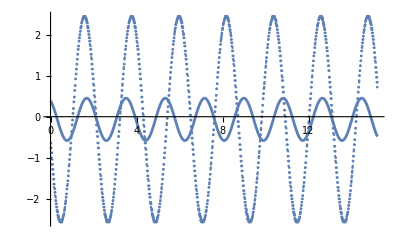

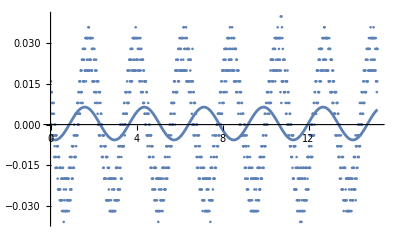

-8.43769×10^-15

-8.52651×10^-14

{{0.515428,0.0639318},{3.44011,0.027345},{2.06495,0.241283},{-0.0645547,0.0448595}}

```mathematica
dat=Import[filenms[[90]]][[5;;-1]];
dat1={#[[1]]/samplerate,#[[2]]}&/@dat[[All,1;;2]];
dat2={#[[1]]/samplerate,#[[2]]}&/@dat[[All,{1,3}]];
fit1 = NonlinearModelFit[dat1, a Sin[b t+ c] + d  , {{a,Max[dat1[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat1,Last][[1,1]]/Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
fit2 = NonlinearModelFit[dat2, a Sin[b t+ c] + d , {{a,Max[dat2[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat2,Last][[1,1]]/Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
Show[ListPlot[{dat2}],Plot[{fit2[t]},{t,0,dat1[[-1,1]]},PlotRange->All]]
Show[ListPlot[{dat1}],Plot[{fit1[t]},{t,0,dat1[[-1,1]]},PlotRange->All]]
Total[fit1["FitResiduals"]]
Total[fit2["FitResiduals"]]
Transpose[{fit2["BestFitParameters"][[All,2]],fit2["ParameterErrors"]}]
```

```mathematica
{}
```

{{0.515428,0.0639318},{0.0344011,0.00027345},{2.06495,0.241283},{-0.0645547,0.0448595}}

{{0.0382655,0.000214789,0.942532,0.0014807,0.537991,0.0126472,0.000196018,0.000159917,-2.49377,0.000799866,0.942443,0.000064447,2.25649,0.000576039,-0.0630178,0.000551623},{0.040389,0.000220246,0.974534,0.00135678,0.281526,0.011606,0.000334305,0.0001601,-2.49412,0.000807916,0.973882,0.0000672509,2.0177,0.000598434,-0.0624431,0.000562253},{-0.0425379,0.000223912,1.00498,0.0012315,15.7405,0.0105747,0.000417703,0.000159683,2.49318,0.00080909,1.00534,0.0000709495,4.91636,0.000627197,-0.0616413,0.000570364},{0.0447688,0.000221218,1.03679,0.00109189,6.0575,0.00943924,0.000285646,0.000155655,2.49268,0.00081552,1.03672,0.0000759676,4.67712,0.00066643,-0.0627916,0.000583499},{0.0472382,0.000234221,1.06836,0.00105223,-0.481998,0.00917389,0.000405441,0.000163749,2.49471,0.000797477,1.06813,0.0000784993,4.43833,0.000683921,-0.0619586,0.00057861},{-0.0498118,0.000223815,1.09952,0.00093594,2.40484,0.00823107,0.000419757,0.000156444,2.49397,0.000806696,1.09959,0.0000825374,4.19847,0.000715791,-0.0627184,0.000590695},{0.052534,0.000226553,1.13066,0.000901826,17.8576,0.0079916,0.000263389,0.000159135,2.49407,0.000818853,1.13094,0.0000847035,3.9591,0.00073339,-0.0622929,0.000600264},{0.0554192,0.000227555,1.16263,0.000880613,17.5913,0.00784687,0.000364454,0.000161304,2.49356,0.000844047,1.16235,0.0000857762,3.72048,0.000743815,-0.062103,0.000614232},{-0.0584335,0.000234826,1.1938,0.00089577,1.62281,0.00800105,0.000388644,0.000168318,2.49336,0.000883016,1.19382,0.0000862162,3.48158,0.000750794,-0.0622166,0.000634402},{0.0615046,0.000224996,1.22554,0.000851862,10.7788,0.00760194,0.000423826,0.000163081,-2.49256,0.000944614,1.2252,0.0000877302,6.38305,0.00076835,-0.0629384,0.000669204},{0.065052,0.00022347,1.25644,0.000829333,4.23336,0.00736823,0.00029022,0.000163254,-2.49247,0.000989682,1.25659,0.0000875435,6.14171,0.000771335,-0.0637181,0.000692861},{0.0686845,0.000225405,1.28811,0.00080939,3.96218,0.0071355,0.000283796,0.000165101,-2.49297,0.00104036,1.28811,0.0000885915,5.90452,0.000784847,-0.064036,0.000722612},{0.0723782,0.000224203,1.31957,0.000765234,3.68879,0.00667913,0.000343639,0.000163658,-2.49126,0.00108742,1.31942,0.0000908018,5.66583,0.000806974,-0.0630452,0.000752863},{0.0765086,0.000227904,1.35063,0.000724588,3.41163,0.00625788,0.000385353,0.000165077,-2.49124,0.00112489,1.35088,0.0000939032,5.42348,0.00083497,-0.0625762,0.000779811},{-0.0806107,0.000223324,1.38244,0.000657429,12.5516,0.00562417,0.000325359,0.000160296,2.48979,0.00113561,1.38227,0.0000966708,8.32544,0.000857741,-0.0606547,0.000791461},{-0.0850729,0.000226054,1.4137,0.000614958,5.98929,0.0052324,0.000376917,0.000161023,2.48929,0.00113916,1.4137,0.000100365,8.08934,0.00088653,-0.062556,0.000800789},{0.0894566,0.000227096,1.44511,0.000575966,21.4031,0.00490045,0.000383028,0.000160971,2.48786,0.00114461,1.44513,0.000105267,1.56293,0.000925104,-0.0621278,0.000813106},{0.093944,0.000229014,1.47664,0.000547927,8.54278,0.00469083,0.000328251,0.000162086,2.48674,0.00113451,1.47657,0.000108798,1.3245,0.000951104,-0.0617701,0.000814311},{0.0984636,0.000223148,1.50799,0.000510657,8.24416,0.00441981,0.000365211,0.000158201,2.4852,0.00113479,1.50797,0.000112304,1.08687,0.000977832,-0.0630229,0.000820715},{0.10296,0.000227196,1.53964,0.000503129,14.221,0.004413,0.000286183,0.000161679,2.48408,0.00115761,1.53936,0.000116092,0.84865,0.0010089,-0.062426,0.000839323},{0.106872,0.000230021,1.57073,0.000498109,1.34299,0.00442251,0.000330265,0.000164317,2.48014,0.0011605,1.57082,0.000115641,0.606751,0.00100538,-0.0619133,0.0008386},{-0.110781,0.000229925,1.6024,0.000483961,16.7311,0.00433573,0.000295795,0.000164425,2.4815,0.00116572,1.6021,0.00011317,0.36557,0.000986249,-0.0624886,0.000835739},{0.11355,0.000228751,1.63375,0.000466434,0.70298,0.00419551,0.000371394,0.000163041,2.47891,0.0011875,1.63363,0.000111309,0.125658,0.00097399,-0.0604833,0.000842877},{0.11581,0.000230038,1.66506,0.000450299,0.382171,0.00404686,0.000344897,0.000162838,-2.47827,0.0012231,1.66506,0.000110447,3.02997,0.000971121,-0.0616326,0.000860022},{0.1172,0.000238661,1.69658,0.000449118,0.0561392,0.0040177,0.000345164,0.000167639,-2.47692,0.00121675,1.6964,0.000106571,2.79156,0.000941085,-0.0622448,0.000849616},{-0.117377,0.000242798,1.71228,0.000450419,3.03281,0.00401702,0.000314408,0.000169984,2.47651,0.00124405,1.71212,0.000107761,12.0953,0.000953173,-0.0619946,0.000866714},{-0.117391,0.000236032,1.7278,0.000433424,9.15526,0.00385357,0.000280497,0.000164847,2.47683,0.00126927,1.72786,0.000109089,11.9767,0.000966181,-0.0629418,0.000883071},{-0.117119,0.000235705,1.74355,0.000430746,2.70518,0.00381854,0.000361533,0.000164355,-2.47673,0.00126398,1.74359,0.000108227,2.42884,0.000959261,-0.061054,0.000878989},{-0.116571,0.00024456,1.75928,0.000447805,2.54335,0.00395975,0.000349081,0.00017045,-2.47695,0.00126946,1.75928,0.000108704,2.31015,0.000963746,-0.0608714,0.000883185},{-0.116299,0.00023281,1.76564,0.000427367,8.76238,0.00377562,0.000428812,0.000162282,-2.47742,0.0012779,1.76546,0.000109531,2.26482,0.000971011,-0.0605898,0.000889424},{0.115921,0.000230127,1.772,0.000424162,24.4048,0.00374439,0.000375226,0.000160456,2.47667,0.00128033,1.77187,0.000109972,11.6393,0.000974811,-0.0618536,0.000891618},{-0.115726,0.000237709,1.77841,0.000439497,2.34492,0.00387737,0.000323621,0.00016581,2.4768,0.00128494,1.77812,0.000110625,11.5898,0.000980425,-0.0629763,0.00089544},{0.115201,0.000231865,1.78437,0.00043158,17.994,0.00380518,0.000294953,0.000161829,2.4752,0.00128635,1.78454,0.000111151,11.5438,0.000984716,-0.0617123,0.000897156},{-0.114774,0.000238843,1.79072,0.000447491,2.22077,0.00394355,0.000254754,0.000166823,-2.47643,0.00127481,1.79069,0.000110478,2.07164,0.000978407,-0.0614454,0.000889918},{0.114475,0.000227055,1.79704,0.000427971,24.1439,0.00377047,0.000276387,0.000158728,2.47663,0.0012746,1.79699,0.000110899,5.16276,0.000981771,-0.0620091,0.000890709},{0.113953,0.000232203,1.80329,0.000441474,24.0815,0.00388802,0.000272861,0.000162495,2.47658,0.00129229,1.80329,0.000112948,5.11639,0.000999336,-0.0622751,0.000904109},{0.113426,0.000227979,1.80959,0.000437475,17.7344,0.00385184,0.000327842,0.000159725,2.47717,0.00127563,1.80961,0.000112023,5.06693,0.000990628,-0.0619332,0.000893582},{0.112973,0.000231688,1.81589,0.000448676,5.10595,0.00394942,0.000282995,0.000162531,2.47663,0.00126413,1.81587,0.000111631,17.5867,0.000986486,-0.0632664,0.000886709},{0.112339,0.000223902,1.82225,0.000438501,5.04246,0.00385918,0.00034472,0.000157288,-2.47659,0.00128026,1.82211,0.0001137,26.9642,0.00100407,-0.0633014,0.000899293},{0.111646,0.00023374,1.82854,0.000463348,4.97659,0.00407798,0.000297249,0.000164441,2.47804,0.00128429,1.82832,0.000114672,4.92571,0.00101192,-0.0608343,0.000903465},{0.11109,0.000233632,1.83435,0.000468142,4.91863,0.00411982,0.000338592,0.0001646,2.4779,0.00127811,1.83466,0.000114852,4.87763,0.00101271,-0.0620987,0.00090053},{-0.110377,0.000228867,1.84087,0.000464666,26.8453,0.00408881,0.000288806,0.000161512,2.47882,0.00127805,1.84089,0.000115546,4.83017,0.00101801,-0.0629703,0.000901933},{0.109728,0.00023266,1.8473,0.0004784,4.78977,0.00420949,0.000249483,0.000164466,2.47713,0.00129309,1.84737,0.000117788,11.0653,0.00103681,-0.0630119,0.000914096},{0.109122,0.000224057,1.85358,0.000466399,4.72395,0.00410434,0.000330602,0.00015865,2.47869,0.0012756,1.85349,0.000116886,4.73335,0.00102814,-0.0616253,0.000903204},{0.108284,0.000231595,1.85993,0.000489145,17.2287,0.0043038,0.000309497,0.000164268,2.47781,0.00128731,1.8598,0.000118804,4.68541,0.00104411,-0.0609522,0.000913035},{0.10768,0.000229625,1.86616,0.000490952,4.60247,0.00431876,0.000337374,0.000163141,2.47811,0.00127195,1.86615,0.000118172,4.63849,0.00103759,-0.0626776,0.000903673},{0.106868,0.000226815,1.87246,0.000491842,4.53935,0.00432606,0.000189617,0.00016141,2.47907,0.00129492,1.87235,0.000121051,4.59207,0.00106194,-0.063907,0.000921503},{0.106045,0.000229762,1.87875,0.000505279,4.47671,0.00444343,0.000318921,0.000163767,2.47845,0.00128332,1.87871,0.000120786,4.54167,0.00105883,-0.0629383,0.000914748},{-0.105333,0.000222844,1.88507,0.000496389,26.4079,0.00436356,0.000225004,0.000159079,2.47936,0.00127641,1.88497,0.000120843,4.49595,0.00105838,-0.0627371,0.000911241},{0.104479,0.000225388,1.89105,0.000508893,4.35747,0.00447212,0.000391414,0.000161114,2.47877,0.00128108,1.89117,0.000122033,4.44713,0.00106807,-0.0622945,0.000915933},{-0.103754,0.000221742,1.89748,0.00050688,26.2859,0.00445246,0.000333597,0.000158723,2.47952,0.00129657,1.8975,0.000124177,4.39922,0.00108601,-0.062902,0.000928328},{0.102785,0.0002177,1.90377,0.000504746,16.8002,0.00443141,0.000360359,0.000156018,2.4806,0.00127653,1.90381,0.000122853,4.35178,0.00107365,-0.0628971,0.000915185},{0.102006,0.000223046,1.90993,0.000523292,10.4587,0.00459135,0.000259036,0.000160017,2.48089,0.0012717,1.91004,0.000122963,4.30456,0.00107391,-0.0629665,0.000912803},{0.101135,0.000221652,1.91661,0.000526499,10.3913,0.00461665,0.000304237,0.000159167,2.48094,0.00129069,1.91631,0.000125336,4.25433,0.00109407,-0.0626896,0.00092741},{0.100411,0.000225335,1.92274,0.00054081,10.3363,0.00473807,0.000236411,0.000161936,2.48119,0.00128266,1.92268,0.000125027,4.20786,0.00109071,-0.0622365,0.000922498},{0.0994852,0.000226012,1.92907,0.000548809,3.9911,0.00480434,0.000268699,0.000162517,2.48184,0.00128708,1.92892,0.00012583,4.15967,0.00109721,-0.0610572,0.00092638},{0.0986732,0.000222646,1.93517,0.00054611,3.93459,0.00477638,0.000284507,0.000160166,2.4815,0.00128975,1.93517,0.000126442,4.11488,0.00110205,-0.0626994,0.000928851},{0.0978878,0.000222431,1.94154,0.000550588,3.87241,0.00481105,0.00032523,0.000160049,2.48251,0.00129704,1.94143,0.000127359,4.06337,0.00110973,-0.0639267,0.00093449},{0.096965,0.000228254,1.94751,0.000570691,3.81559,0.00498196,0.00018415,0.000164252,2.48286,0.00130969,1.94773,0.000128763,4.01646,0.00112164,-0.0638116,0.000943841},{0.0216579,0.00244111,2.54182,0.0247403,2.43503,0.217297,-0.00102898,0.00171069,2.4816,0.00131402,1.96347,0.000129329,3.89551,0.00112617,-0.0626126,0.000946779},{0.0207159,0.00238755,2.55719,0.0252305,2.27421,0.221976,-0.000864635,0.00167251,2.48335,0.0013092,1.97919,0.000128321,3.77639,0.00111752,-0.0628703,0.000942087},{-0.0905009,0.000219694,1.99476,0.000581013,12.8018,0.00503156,0.000357534,0.00015748,0.538907,0.0641053,2.56988,0.0258081,2.42635,0.228028,-0.0667314,0.0448025},{-0.0883576,0.000221076,2.01045,0.000593246,6.37389,0.00512613,0.000392083,0.000158067,-2.48522,0.00137188,2.01062,0.000132025,6.67815,0.00115155,-0.0632655,0.000981932},{0.0840528,0.000223766,2.04221,0.000617502,28.081,0.00532346,0.000301543,0.000159076,-2.48622,0.00140946,2.0421,0.000131929,6.43928,0.0011542,-0.0620878,0.00100125},{-0.080018,0.00022775,2.07352,0.000646271,5.8099,0.00557814,0.00035203,0.000161064,-2.48714,0.00148316,2.07343,0.00013465,6.19921,0.00118231,-0.0627121,0.00104557},{0.0762513,0.000230751,2.10499,0.000675747,33.8096,0.00586232,0.000331447,0.000162551,-2.48947,0.00153697,2.10482,0.000135755,5.96005,0.00119637,-0.0621911,0.00107682},{0.0725549,0.000229516,2.13636,0.000699677,20.9745,0.00611846,0.000319773,0.000161346,-0.489768,0.0613265,2.7392,0.0295861,4.27545,0.258811,-0.0598467,0.0438033},{0.0691505,0.000229359,2.16728,0.000732472,8.14704,0.00646269,0.000241527,0.000161207,2.49141,0.00162335,2.16765,0.000140002,8.62442,0.00123884,-0.062286,0.00113231},{-0.0658148,0.00023042,2.1991,0.000777903,4.73463,0.00692032,0.000228294,0.000162215,2.49222,0.00164808,2.19907,0.000143132,8.38167,0.00126606,-0.062705,0.00115207},{0.0626217,0.000224764,2.23046,0.0008057,13.9013,0.00720673,0.000247197,0.000158635,2.49329,0.00165282,2.23058,0.000146151,8.14264,0.00129018,-0.0601745,0.00116082},{0.0597506,0.000226194,2.2617,0.000860019,1.07433,0.00770534,0.000369806,0.000160118,2.4941,0.00164372,2.26191,0.00014905,1.61857,0.00131186,-0.0620779,0.00116178},{0.0569984,0.000224925,2.29366,0.000906097,7.09916,0.00809614,0.000293355,0.000159648,2.49441,0.0016495,2.2933,0.000153676,1.37902,0.00134792,-0.0628696,0.0011738},{0.0544558,0.000227349,2.32476,0.000966059,19.421,0.00857621,0.000312516,0.000161693,2.49523,0.00165327,2.3248,0.00015753,1.14415,0.00137721,-0.0640982,0.0011832},{0.0520511,0.000228651,2.35629,0.00101993,0.316497,0.0089746,0.00025739,0.000162778,2.49689,0.00166524,2.35609,0.000160623,0.903525,0.00140146,-0.0630487,0.0011954},{-0.0497002,0.000224138,2.38838,0.00104683,22.0512,0.00912277,0.000353412,0.000159574,2.49761,0.00168083,2.38764,0.000162104,0.660716,0.00141347,-0.0626375,0.00120607},{0.0475542,0.000221137,2.41902,0.00107653,-0.177099,0.00930905,0.000471884,0.000157337,0.533429,0.0641363,2.99668,0.0262508,-0.827647,0.231783,-0.0616779,0.0448937},{-0.0455023,0.000224385,2.45022,0.00113525,9.00235,0.0097719,0.000260641,0.000159419,-2.49832,0.00171761,2.45046,0.000160117,-2.9572,0.00140054,-0.0609898,0.0012207},{0.0435076,0.000221789,2.48203,0.0011653,37.0275,0.0100285,0.000314007,0.000157279,-2.49919,0.00174297,2.48186,0.000158401,3.08437,0.00138958,-0.0633674,0.00123078},{-0.0417696,0.000218553,2.51287,0.00118775,2.23266,0.0102643,0.000261254,0.000154689,-2.50104,0.00171225,2.51329,0.000151935,2.84318,0.00133701,-0.0625117,0.00120242},{-0.0399938,0.00021989,2.5446,0.0012407,8.27406,0.0108043,0.000329379,0.000155379,-2.49995,0.00178574,2.54469,0.000155943,2.60676,0.00137597,-0.062393,0.00124949},{-0.0383729,0.000222897,2.5755,0.00130707,1.75393,0.0114837,0.000376137,0.00015737,-2.50142,0.00179933,2.57613,0.000156003,2.36673,0.00137853,-0.0606152,0.00125752},{-0.0034597,0.000975984,1.16214,0.0640474,9.12888,0.5484,-0.000750548,0.000699692,2.50099,0.00179975,2.60754,0.000156738,5.26657,0.00138514,-0.0615888,0.00125953},{0.0354792,0.000215792,2.63833,0.00137423,4.41767,0.0122514,0.000338959,0.000152475,2.50082,0.00180167,2.63893,0.000159137,5.0269,0.00140451,-0.0632142,0.00126542},{0.0340385,0.00022007,2.67015,0.00146904,16.7481,0.0131301,0.000241761,0.000155707,2.50245,0.00182007,2.67029,0.000164032,4.79049,0.00144414,-0.063733,0.00128498},{0.0327349,0.000221908,2.70099,0.00155028,35.3688,0.0138359,0.000300775,0.000157262,2.50217,0.00180628,2.7018,0.000166626,4.55071,0.00146268,-0.0620963,0.00128265},{0.0313626,0.000215649,2.73266,0.00158216,16.2837,0.0140486,0.000245761,0.000153071,2.50275,0.00181334,2.73311,0.000170644,4.31026,0.00149387,-0.0619225,0.00129417},{-0.0303159,0.000217559,2.76491,0.00165836,19.1831,0.0146122,0.000310589,0.000154606,2.50373,0.00181983,2.7646,0.000173371,4.06772,0.00151464,-0.0617528,0.0013028},{0.0289993,0.000222766,2.79581,0.00177881,9.53237,0.0155454,0.000266451,0.000158398,2.50377,0.00185421,2.79608,0.000177023,3.83089,0.00154507,-0.0598207,0.00132772},{0.000136506,0.000752202,282.99,1.25789,531.199,11.0313,-5.29855×10^-6,0.000532105,2.50424,0.00188457,2.82744,0.000178337,3.59398,0.00155725,-0.0628162,0.00134593},{0.00607162,0.000707093,2.2679,0.0265092,29.3779,0.237094,0.000394614,0.000500765,0.515428,0.0639318,3.44011,0.027345,2.06495,0.241283,-0.0645547,0.0448595},{-0.00280507,0.000697306,1.44907,0.0570971,1.22489,0.511203,0.000459368,0.000496094,-0.499434,0.0634732,3.47599,0.0284095,4.93784,0.250333,-0.0614941,0.0446939},{-0.00252265,0.000671598,1.47036,0.0624292,7.30937,0.557168,0.00059891,0.000480338,-2.50464,0.00208368,2.92165,0.000185895,6.01211,0.00163416,-0.0613441,0.00146579},{-0.00242408,0.000647932,1.49503,0.0636287,19.6306,0.564786,0.000596209,0.000465241,2.505,0.00211344,2.95309,0.000185632,8.91712,0.00163598,-0.0611107,0.0014815},{0.0232564,0.000228502,2.98427,0.00219578,8.17703,0.0192908,0.000199567,0.000160955,2.50569,0.00214497,2.98447,0.00018697,8.68193,0.00165041,-0.0647677,0.00150139}}

```mathematica
Differences[Select[dat2,#[[2]]>0.90 Max[dat2[[All,2]]]&][[All,1]]]
```

```mathematica
Select[dat2,#[[2]]>0.90 Max[dat2[[All,2]]]&][[All,1]]
Differences[Select[dat2,#[[2]]>0.90 Max[dat2[[All,2]]]&][[All,1]]]
```

{168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,198,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,620,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,830,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1040,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1252,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1462}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2}

```mathematica
D[Sin[ω t + ϕ],{t,2}]
```

-ω^2 Sin[ϕ+t ω]

```mathematica
Solve[{Cos[ϕ+t ω]==0,Sin[ϕ+t ω]<0},ϕ]
```

{{ϕ→ConditionalExpression[1/2 (-π-2 t ω+4 π C[1]), C[1]∈ℤ]},{ϕ→ConditionalExpression[1/2 (-π-2 t ω+4 π (C[1]-C[2])), (C[1]|C[2])∈ℤ&&C[1]≥0&&C[2]≥0]}}

192

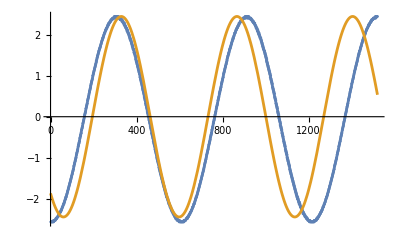

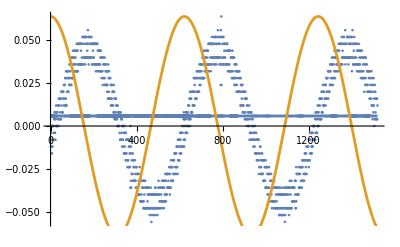

```mathematica
rl1=Evaluate[{a->Max[dat2[[All,2]]],b->0.9 2 π /Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]],c->-2π MaximalBy[dat2,Last][[1,1]]/Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]+π/2,d->0}];
rl2=Evaluate[{a->Max[dat1[[All,2]]],b->0.9 2 π /Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]],c->-2π MaximalBy[dat1,Last][[1,1]]/Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]+π/2,d->0}];
Show[ListPlot[{dat2}],Plot[{fit2[t],(a Sin[b t+ c] + d)/.rl1},{t,0,dat1[[-1,1]]},PlotRange->All]]
Show[ListPlot[{dat1}],Plot[{fit1[t],(a Sin[b t+ c] + d)/.rl2},{t,0,dat1[[-1,1]]},PlotRange->All]]
```

```mathematica
Max[Differences[Select[dat1,#[[2]]>0.90 Max[dat1[[All,2]]]&][[All,1]]]]
```

-∞

```mathematica
Differences[Select[dat1,#[[2]]>0.90 Max[dat1[[All,2]]]&][[All,1]]]
```

{}

```mathematica
Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&]
```

{{148,0.052},{152,0.052},{154,0.052},{156,0.052},{158,0.052},{162,0.052},{164,0.052},{166,0.052},{174,0.056},{176,0.052},{178,0.052},{182,0.052},{188,0.052},{190,0.052},{750,0.052},{760,0.052},{764,0.052},{766,0.052},{768,0.052},{776,0.052},{778,0.056},{780,0.052},{786,0.052},{790,0.052},{792,0.056},{794,0.064},{796,0.052},{798,0.052},{802,0.052},{804,0.052},{1354,0.052},{1362,0.052},{1364,0.052},{1370,0.056},{1378,0.052},{1380,0.052},{1382,0.052},{1384,0.052},{1388,0.052},{1394,0.052},{1398,0.052},{1402,0.052},{1404,0.056},{1412,0.052}}